## 出身階層間の教育達成格差

```mathematica
Module[{x,score1,score2,overall,n=20(*各階層人数*)},
x=15;(* 進学可能人数 *)
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
(* {上層出身者の成績, 階層index=1}*)
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*　{下層出身者の成績, 階層index=0*)
Print["score1=",score1];
Print["score2=",score2];
overall=Flatten[{score1,score2},1];(*リストの結合*)
overall=Sort[overall,#1[[1]]>#2[[1]]&];(*成績順に並び替え *)
Table[overall[[i]][[2]],{i,1,x}]](* 進学者の階層を表示．1が高階層出身者．0が低階層 *)
```

score1={{52.4682,1},{50.7726,1},{51.1559,1},{54.1062,1},{51.9829,1},{50.3526,1},{50.4204,1},{50.7304,1},{50.093,1},{49.2319,1},{53.9514,1},{51.7565,1},{52.7942,1},{53.2419,1},{52.0125,1},{51.6454,1},{53.3385,1},{51.4227,1},{51.2127,1},{52.5856,1}}

score2={{50.2682,0},{49.3288,0},{49.3301,0},{48.2329,0},{49.7341,0},{50.8821,0},{51.349,0},{50.1607,0},{49.7235,0},{48.4856,0},{49.2978,0},{50.7573,0},{50.9468,0},{48.7765,0},{48.1327,0},{49.9159,0},{50.4359,0},{48.6969,0},{50.5476,0},{50.222,0}}

{1,1,1,1,1,1,1,1,1,1,1,1,0,1,1}

## オッズ比と相対リスク比の比較

```mathematica
(*　オッズ比　と相対リスク比を出力する関数*)
```

```mathematica
edu2[x_,n_,out_]:=Module[{score1,score2,overall,ad,r1,r2,odds,rr},
score1=Table[{RandomReal[NormalDistribution[52,1]],1},{n}];
score2=Table[{RandomReal[NormalDistribution[50,1]],0},{n}];
(*Print["score1=",score1];Print["score2=",score2];*)
overall=Flatten[{score1,score2},1];
overall=Sort[overall,#1[[1]]>#2[[1]]&];
ad=Total[Table[overall[[i]][[2]],{i,1,x}]];
r1=(ad)/(n-ad)(* 上層進学オッズ  *);
r2=(x-ad)/(n-(x-ad))(* 下層進学オッズ *);
odds=r1/r2;(* オッズ比 *)
r1=(ad)/n(* 上層進学率  *);
r2=(x-ad)/n(* 下層進学率 *);
rr=r1/r2;(* 相対リスク比 *)
If[out==0,odds,rr]
]
```

Power::infy: 無限式1/0が見付かりました．

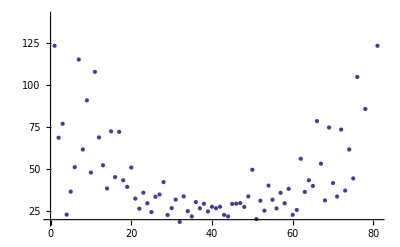

```mathematica
ListPlot[Table[edu2[x,500,0],{x,100,900,10}]]
```

Power::infy: 無限式1/0が見付かりました．

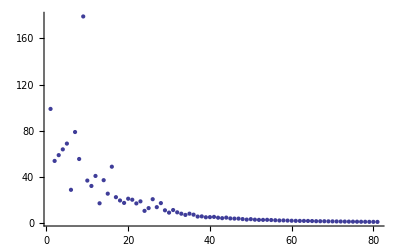

```mathematica
ListPlot[Table[edu2[x,500,1],{x,100,900,10}]]
```

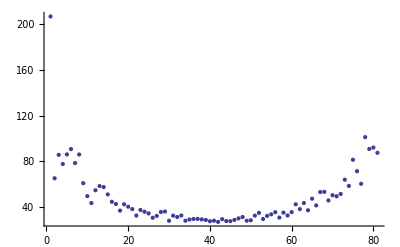

```mathematica
ListPlot[Table[edu2[x,5000,0],{x,1000,9000,100}]]
```

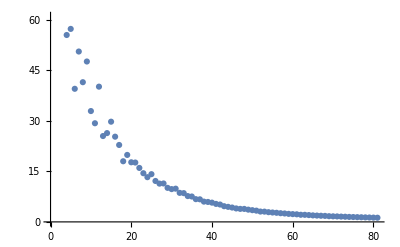

```mathematica
ListPlot[Table[edu2[x,5000(*各人数*),1],{x,1000,9000,100}]]
```